```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"];
```

```mathematica
Integrate[(y^2-x^2)x Exp[-3/2 x^2],{x,0,y}]
```

1/9 (-2+2 ⅇ^(-(3 y^2)/2)+3 y^2)

```mathematica
Integrate[1/(1+b x)^2,{x,1-a,a}]
```

ConditionalExpression[(1-2 a)/((1+a b) (-1-b+a b)),Re[(1+b-a b)/(b-2 a b)]>1||Re[(1+b-a b)/(b-2 a b)]<0||(1+b-a b)/(b-2 a b)∉ℝ]

```mathematica
(*Integrate[(y^2-x^2)1/(1+b y^2/(x^2+y^2))1/(1+b x^2/(x^2+y^2))x Exp[-3/2 x^2],{x,0,y}]*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=287.8*10^3;(*in m/sec*)
G=6.67*10^-11;(*in SI*)
ρ=10^11;(*in kg/m^3*)
clight=3 10^8(*m/sec*);
ρx=10^6*0.3;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
mn=12;(*in GeV*)
t=3 10^17(*Age in sec*);
```

```mathematica
n=10^36;(*in m^-3*)
βplus[mx_?NumericQ]:=(4*mn *mx)/(mn+mx)^2;
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*n)^(1/3);
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
vth[mx_,T_]:=4/3*π*rth[mx,T]^3;
```

```mathematica
fMBboosted[u_]:=(3/(2 vbar^2))^(3/2)4/(√π)u^2 Exp[-3/(2 vbar^2)u^2](*Exp[-η^2] Sinh[2 (√(3/(2 vbar^2))u) η]/(2(√(3/(2 vbar^2))u) η)*) ;
```

```mathematica
g1[u_?NumericQ,mx_?NumericQ,mphi_?NumericQ]:=(vesc^2-u^2)/(vesc^2+u^2)(1+mx^2/mphi^2((u^2+vesc^2)/clight^2))/((1+mx^2/mphi^2(u/clight)^2)(1+mx^2/mphi^2(vesc/clight)^2));
```

```mathematica
CA[sigmaV_,mx_,T_]:=sigmaV/vth[mx,T]
```

```mathematica
y=vesc/vbar;
```

```mathematica
Cself[sigmaSelf_,mx_]:=1/3 √(6/π)ρx/mx sigmaSelf vbar(3 y^2+2Exp[-3/2 y^2]-2)
```

```mathematica
Cselfgeneral[sigmaSelf_,mx_,mphi_]:=sigmaSelf ρx/mx NIntegrate[fMBboosted[u]/u(u^2+vesc^2)(g1[u,mx,mphi]),{u,0,vesc}];
```

```mathematica
LDM[sigmaSelf_,sigmaV_,mx_,T_]:=mx (Cself[sigmaSelf,mx])^2/CA[sigmaV,mx,T]
```

```mathematica
LDMgen[sigmaSelf_?NumericQ,sigmaV_?NumericQ,mx_?NumericQ,mphi_,T_]:=mx (Cselfgeneral[sigmaSelf,mx,mphi])^2/CA[sigmaV,mx,T]
```

```mathematica
Cself[10^-30,10^1.]
```

5.17806×10^-18

```mathematica
Cselfgeneral[10^-38,10^4.,10.]
```

3.56418×10^-29

```mathematica
LDMgen[10^-28,10^-38,1000,1,10^7]
```

1.27808×10^17

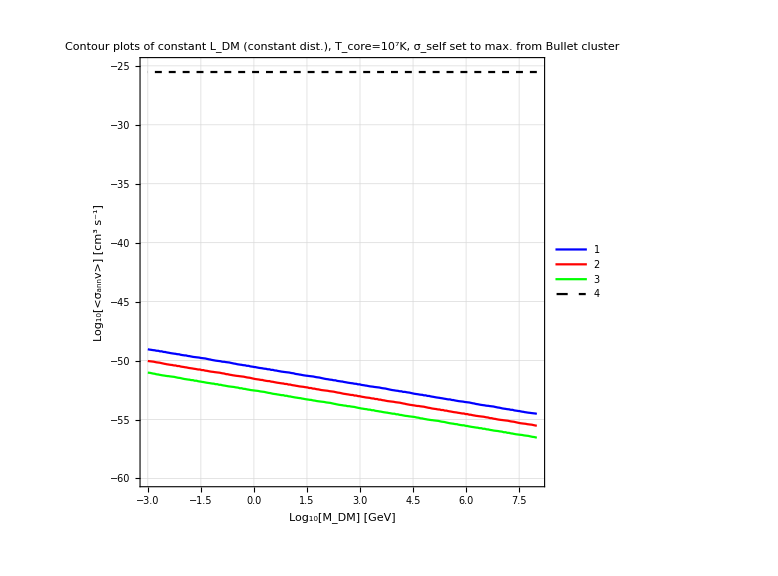

```mathematica
cntrplot1=ContourPlot[{LDM[(10^mdm) 10^-28,10^sigmaV 10^6,10^mdm,10^7]==3 10^31,LDM[(10^mdm) 10^-28,10^sigmaV 10^6,10^mdm,10^7]==3 10^32,LDM[(10^mdm) 10^-28,10^sigmaV 10^6,10^mdm,10^7]==3 10^33,sigmaV==Log10[3*10^-26]},{mdm,-3,8},{sigmaV,-25,-60},PlotLegends->Automatic,ContourLabels->All,Frame->True,FrameStyle->Directive[14,"Times",Black],FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["Log_10[<σ_annv>] [cm^3 s^-1]",FontSize->20,Bold]},ImageSize -> Large,PlotLabel->Style["Contour plots of constant L_DM (constant dist.), T_core=10^7K, σ_self set to max. from Bullet cluster",FontSize->8,Bold],GridLines->Automatic,ContourStyle->{{Thick,Blue},{Thick,Red},{Thick,Green},{Thick,Dashed,Black}}]
```

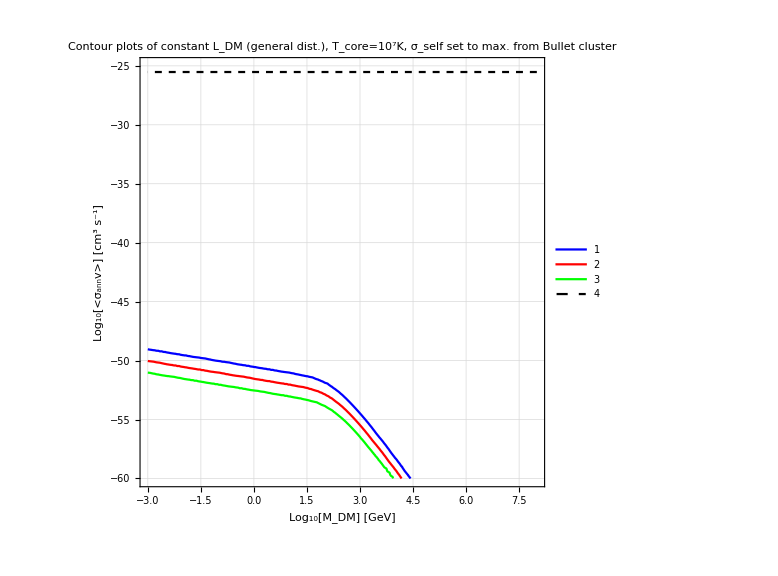

```mathematica
cntrplot2=ContourPlot[{LDMgen[(10^mdm) 10^-28,10^sigmaV 10^6,10^mdm,0.1,10^7]==3 10^31,LDMgen[(10^mdm) 10^-28,10^sigmaV 10^6,10^mdm,0.1,10^7]==3 10^32,LDMgen[(10^mdm) 10^-28,10^sigmaV 10^6,10^mdm,0.1,10^7]==3 10^33,sigmaV==Log10[3*10^-26]},{mdm,-3,8},{sigmaV,-25,-60},PlotLegends->Automatic,ContourLabels->All,Frame->True,FrameStyle->Directive[14,"Times",Black],FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["Log_10[<σ_annv>] [cm^3 s^-1]",FontSize->20,Bold]},ImageSize -> Large,PlotLabel->Style["Contour plots of constant L_DM (general dist.), T_core=10^7K, σ_self set to max. from Bullet cluster",FontSize->8,Bold],GridLines->Automatic,ContourStyle->{{Thick,Blue},{Thick,Red},{Thick,Green},{Thick,Dashed,Black}}]
```

```mathematica
(*cntrplot3=ContourPlot[Log10[LDMgen[(10^mdm) 10^-28,10^sigmaV 10^6,10^mdm,0.1,10^7]],{mdm,-3,8},{sigmaV,-25,-50},PlotLegends->Automatic,FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["Log_10[<σ_annv>] [cm^3 s^-1]",FontSize->20,Bold]},ImageSize -> Large,PlotLabel->Style["Contour plots of constant L_DM (general dist.), T_core=10^7K, σ_self set to max. from Bullet cluster",FontSize->8,Bold],ContourLabels->True,ImageSize->Large]*)
```

```mathematica
(*Export["contour3.pdf",cntrplot3];*)
```

```mathematica
LDM[(10^-1) 10^-2 1.8 10^-28,3 10^-38,10^-2,10^7]
```

9.21288×10^23

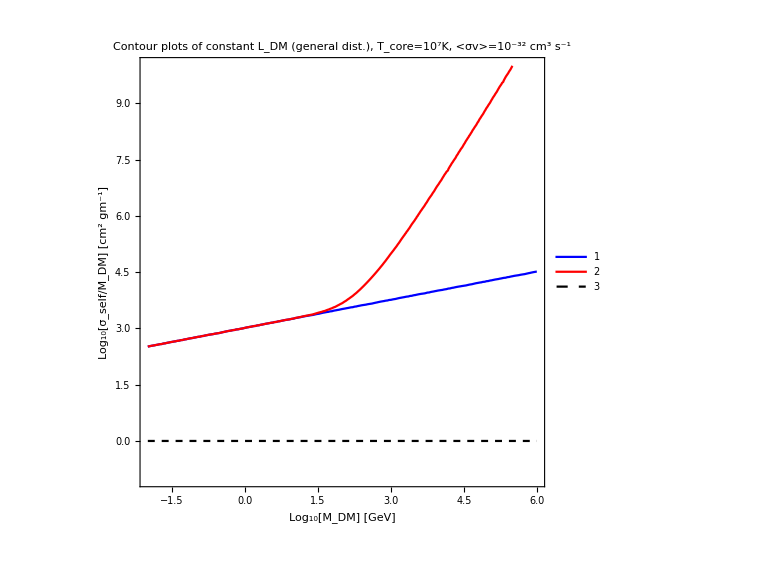

```mathematica
cntrplot4=ContourPlot[{LDM[(10^x)( 10^mdm)( 1.8 10^-28),3 10^-38,10^mdm,10^7]==10^31,LDMgen[(10^x) (10^mdm) (1.8 10^-28),3 10^-38,10^mdm,0.1,10^7]==10^31,x==0},{mdm,-2,6},{x,-1,10},PlotLegends->Automatic,ContourLabels->All,Frame->True,FrameStyle->Directive[14,"Times",Black],FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["Log_10[σ_self/M_DM] [cm^2 gm^-1]",FontSize->20,Bold]},ImageSize -> Large,PlotLabel->Style["Contour plots of constant L_DM (general dist.), T_core=10^7K, <σv>=10^-32 cm^3 s^-1",FontSize->8,Bold],GridLines->None,ContourStyle->{{Thick,Blue},{Thick,Red},{Thick,Dashed,Black}}]
```

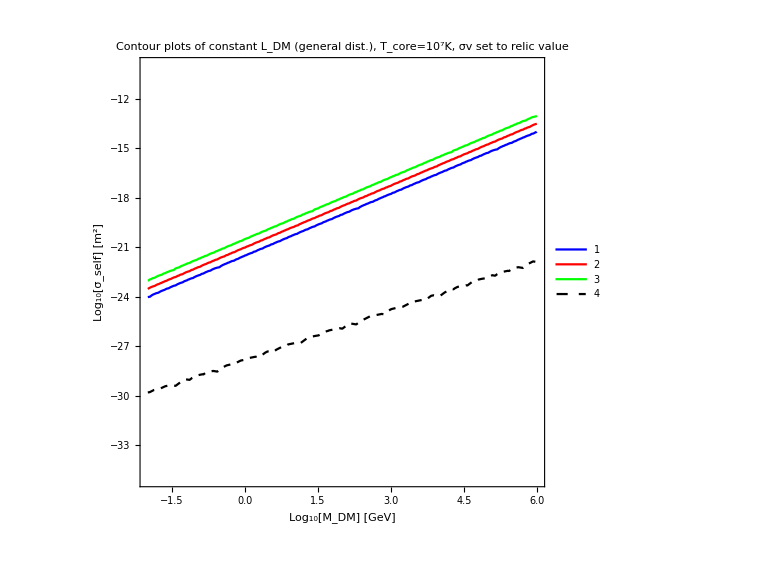

```mathematica
cntrplot5=ContourPlot[{LDM[(10^sigmaSelf),3 10^-32,10^mdm,10^7]==3 10^31,LDM[(10^sigmaSelf),3 10^-32,10^mdm,10^7]==3 10^32,LDM[(10^sigmaSelf),3 10^-32,10^mdm,10^7]==3 10^33,10^sigmaSelf/10^mdm==1.8 10^-28},{mdm,-2,6},{sigmaSelf,-10,-35},PlotLegends->Automatic,ContourLabels->All,Frame->True,FrameStyle->Directive[14,"Times",Black],FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["Log_10[σ_self] [m^2]",FontSize->20,Bold]},ImageSize -> Large,PlotLabel->Style["Contour plots of constant L_DM (general dist.), T_core=10^7K, σv set to relic value",FontSize->8,Bold],GridLines->None,ContourStyle->{{Thick,Blue},{Thick,Red},{Thick,Green},{Thick,Dashed,Black}}]
```

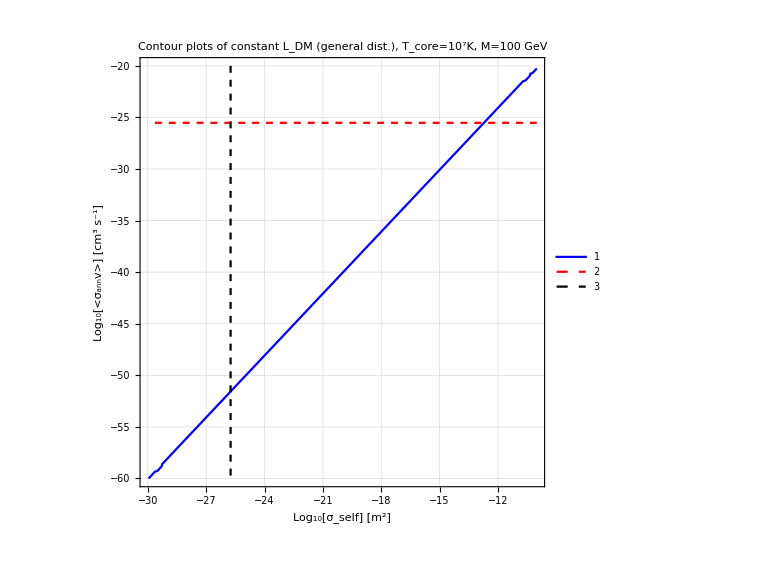

```mathematica
cntrplot6=ContourPlot[{LDMgen[10^sigmaSelf,10^sigmaV 10^6,10^2,0.1,10^7]==10^32,sigmaV==Log10[3*10^-26],sigmaSelf==Log10[10^2 1.8 10^-28]},{sigmaSelf,-10,-30},{sigmaV,-20,-60},PlotLegends->Automatic,ContourLabels->All,Frame->True,FrameStyle->Directive[14,"Times",Black],FrameLabel->{Style["Log_10[σ_self] [m^2]",FontSize->20,Bold],Style["Log_10[<σ_annv>] [cm^3 s^-1]",FontSize->20,Bold]},ImageSize -> Large,PlotLabel->Style["Contour plots of constant L_DM (general dist.), T_core=10^7K, M=100 GeV",FontSize->8,Bold],GridLines->Automatic,ContourStyle->{{Thick,Blue},{Thick,Dashed,Red},{Thick,Dashed,Black}}]
```

```mathematica
(*cntrplot7=ContourPlot[Log10[LDMgen[10^sigmaSelf,10^sigmaV 10^6,10^2,0.1,10^7]],{sigmaSelf,-20,-50},{sigmaV,-25,-60},PlotLegends->None,ContourLabels->True,Frame->True,FrameStyle->Directive[14,"Times",Black],FrameLabel->{Style["Log_10[σ_self] [m^2]",FontSize->20,Bold],Style["Log_10[<σ_annv>] [cm^3 s^-1]",FontSize->20,Bold]},ImageSize -> Large,PlotLabel->Style["Contour plots of constant L_DM (general dist.), T_core=10^7K, M=100 GeV",FontSize->8,Bold],GridLines->Automatic]*)
```

```mathematica
(*Export["contour7.pdf",cntrplot7];*)
```